# Set ODE model

```mathematica
Clear[Neu]
```

```mathematica
model = ParametricNDSolve[{
Neu'[t]==lamdaNB + KNB*B[t]-muN*Neu[t]-vNM*Neu[t]*M[t],
M'[t]==lamdaM+KMB*B[t]-muM*M[t],
B'[t]==(sBN*Neu[t])/(1+iBM)-muB*B[t],
A'[t]==sAM*M[t]-muA*A[t],
A[0]==0,
B[0]==0,
Neu[0]==0,
M[0]==0
},
{Neu,M,B,A},
{t,0,72},
{lamdaNB,KNB,muN, vNM,lamdaM, KMB, muM,sBN,muB,iBM,sAM,muA}]
```

{Neu→ParametricFunction[<>],M→ParametricFunction[<>],B→ParametricFunction[<>],A→ParametricFunction[<>]}

```mathematica
newModel={Neu,M,B,A}/.model
```

{ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>]}

# Interpolate values

## For cytokines, t=0.5,2 and 120 are missing. 120 is out of range for interpolation.

```mathematica
cyBRawData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCytokines.csv",{"Data",2;;6,2;;3 }]
```

{{0.25,1.8725},{1,4.01255},{4,29.17},{6,7.365},{12,5.985}}

```mathematica
Bfit = Interpolation[cyBRawData,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[…]

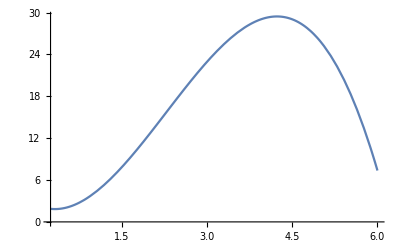

```mathematica
Plot[Bfit[x],{x,0.25,6}]
```

```mathematica
{x,Bfit[x]}/.x->{0.5,2}
```

{{0.5,2},{1.99567,12.6939}}

```mathematica
cyARawData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCytokines.csv",{"Data",-8;;-4,2;;3 }]
```

{{0.25,0.96225},{1,1.0565},{4,13.88},{6,8.6005},{12,7.4845}}

```mathematica
Afit=Interpolation[cyARawData,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[…]

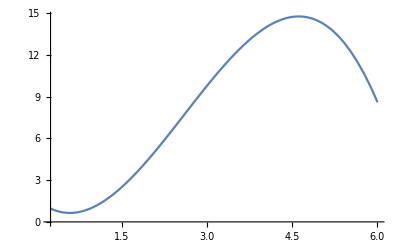

```mathematica
Plot[Afit[x],{x,0.25,6}]
```

```mathematica
{x,Afit[x]}/.x->{0.5,2}
```

{{0.5,2},{0.665976,4.63346}}

## For cells, t=0.25 and 12 are missing. 0.25 is of range for interpolation.

```mathematica
cellNeuRawData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCell.csv",
{"Data", 2;;9,2;;3}]
```

{{0.5,1.85},{1,10.7083},{2,26.52},{4,22.3333},{6,16.6},{24,6.80769},{48,5.85185},{72,0.555556}}

```mathematica
Neufit=Interpolation[cellNeuRawData,InterpolationOrder->2,Method->"Spline"]
```

InterpolatingFunction[…]

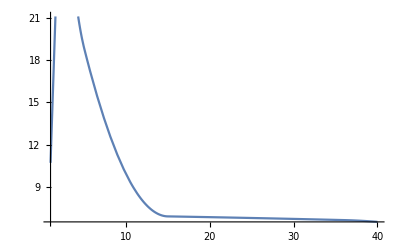

```mathematica
Plot[Neufit[x],{x,1,40.}]
```

```mathematica
Neufit[12]
```

8.00644

```mathematica
cellMRawData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCell.csv",
{"Data", -11;;-3,2;;3}]
```

{{72,0.555556},{120,0.344828},{0.5,0.333333},{1,1.08},{2,3.27586},{4,4.83333},{6,12.6522},{24,18.7667},{48,19.5652}}

```mathematica
Mfit=Interpolation[cellMRawData,InterpolationOrder->1,Method->"Spline"]
```

InterpolatingFunction[…]

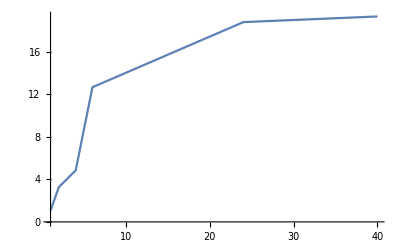

```mathematica
Plot[Mfit[x],{x,1,40.}]
```

```mathematica
Mfit[12]
```

14.6903

# Import interpolated data and fit

```mathematica
NeuData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCell_i.csv",
{"Data", 2;;10,2;;3}]
```

{{0.5,1.85},{1,10.7083},{2,26.52},{4,22.3333},{6,16.6},{12,8.00644},{24,6.80769},{48,5.85185},{72,0.555556}}

```mathematica
MData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCell_i.csv",
{"Data", 11;;,2;;3}]
```

{{0.5,0.333333},{1,1.08},{2,3.27586},{4,4.83333},{6,12.6522},{12,14.6903},{24,18.7667},{48,19.5652},{72,14.2759}}

```mathematica
AData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCytokines_i.csv",{"Data",11;;,2;;3 }]
```

{{0.5,0.665976},{1,1.0565},{2,4.63346},{4,13.88},{6,8.6005},{12,7.4845},{24,3.06008},{48,6.56325},{72,5.7875}}

```mathematica
BData=Import["/Users/chaolinhan/OneDrive/PostgraduateProject/data/tidydataCytokines_i.csv",{"Data",2;;10,2;;3 }]
```

{{0.5,1.99567},{1,4.01255},{2,12.6939},{4,29.17},{6,7.365},{12,5.985},{24,8.76},{48,1.07642},{72,0.764}}

```mathematica
NeuData=Transpose[NeuData];
MData = Transpose[MData];
BData=Transpose[BData];
AData=Transpose[AData];
```

```mathematica
fitData=NeuData~Join~MData~Join~BData~Join~AData
```

{{0.5,1,2,4,6,12,24,48,72},{1.85,10.7083,26.52,22.3333,16.6,8.00644,6.80769,5.85185,0.555556},{0.5,1,2,4,6,12,24,48,72},{0.333333,1.08,3.27586,4.83333,12.6522,14.6903,18.7667,19.5652,14.2759},{0.5,1,2,4,6,12,24,48,72},{1.99567,4.01255,12.6939,29.17,7.365,5.985,8.76,1.07642,0.764},{0.5,1,2,4,6,12,24,48,72},{0.665976,1.0565,4.63346,13.88,8.6005,7.4845,3.06008,6.56325,5.7875}}

```mathematica
fitData=Delete[fitData,{{3},{5},{7}}];
fitData=Transpose[fitData]
```

{{0.5,1.85,0.333333,1.99567,0.665976},{1,10.7083,1.08,4.01255,1.0565},{2,26.52,3.27586,12.6939,4.63346},{4,22.3333,4.83333,29.17,13.88},{6,16.6,12.6522,7.365,8.6005},{12,8.00644,14.6903,5.985,7.4845},{24,6.80769,18.7667,8.76,3.06008},{48,5.85185,19.5652,1.07642,6.56325},{72,0.555556,14.2759,0.764,5.7875}}

```mathematica
Export["/Users/chaolinhan/OneDrive/PostgraduateProject/data/iData.csv",fitData,"CSV"]
```

/Users/chaolinhan/OneDrive/PostgraduateProject/data/iData.csv

```mathematica
LSFit=FindFit[fitData,
{newModel[[1]],newModel[[2]],newModel[[3]],newModel[[4]]},
{lamdaNB,KNB,muN, vNM,lamdaM, KMB, muM,sBN,muB,iBM,sAM,muA},
t]
```

FindFit::fitc: Number of coordinates (5) is not equal to the number of variables (1).

FindFit[{{0.5,1,4,12,48,72},{1.85,10.7083,22.3333,8.00644,5.85185,0.555556},{0.333333,1.08,4.83333,14.6903,19.5652,14.2759},{1.99567,4.01255,29.17,5.985,1.07642,0.764},{0.665976,1.0565,13.88,7.4845,6.56325,5.7875}},{ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>],ParametricFunction[<>]},{lamdaNB,KNB,muN,vNM,lamdaM,KMB,muM,sBN,muB,iBM,sAM,muA},t]